# 2d Voronoi bidisperse rigidity

## data load

```mathematica
p0s=Table[i,{i,3.78,3.90,0.01}]
```

{3.78,3.79,3.8,3.81,3.82,3.83,3.84,3.85,3.86,3.87,3.88,3.89,3.9}

```mathematica
fraction=Table[i,{i,0.5,1.0,0.1}]
```

{0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
sizeRatio = Table[i,{i,1.0,1.24,0.02}]
```

{1.,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24}

```mathematica
rawData=Table[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/2dVoronoiBidisperse/maxForce&ShearModulus_N1024_p","_KA0.0000_sizeRatio","_fraction",".nc.nc"},{p0s[[p]],sizeRatio[[r]],fraction[[f]]},{3,3,3}],"Data"],{p,Length[p0s]}],{r,Length[sizeRatio]}],{f,Length[fraction]}];
```

Import::format: Cannot import data as Data.

```mathematica
{fraction[[3]],sizeRatio[[1]],p0s[[6]]}
```

{0.7,1.,3.83}

```mathematica
Position[rawData,$Failed]
```

{{3,11,6}}

```mathematica
Normal[rawData[[1,2,1,2]]]
```

{0.0337523,0.0368518,0.0372299,0.042044,0.040353,0.0296295,0.0447813,0.0498839,0.0975715,0.043842}

```mathematica
Count[Normal[rawData[[1,2,1,2]]],x_/;x>10^(-10)]
```

10

```mathematica
rigidRatio=Table[Table[Table[If[Length[rawData[[f,r,p]]]>1,Count[Normal[rawData[[f,r,p,2]]],x_/;x>10^(-10)]/Length[Normal[rawData[[f,r,p,2]]]],0],{p,Length[p0s]}],{r,Length[sizeRatio]}],{f,Length[fraction]}];
```

```mathematica
rigidRatio[[1,1,3]]
```

1/10

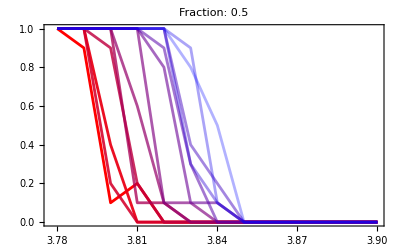
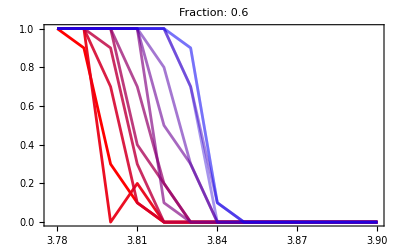
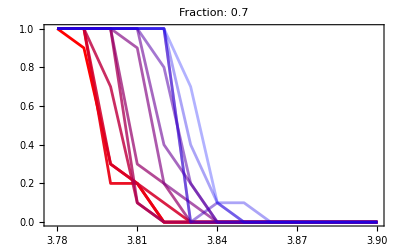
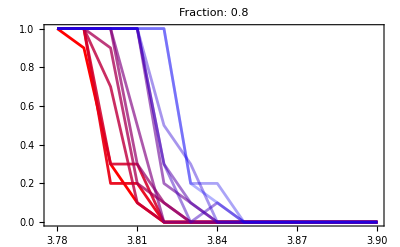
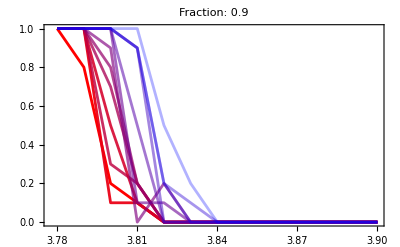
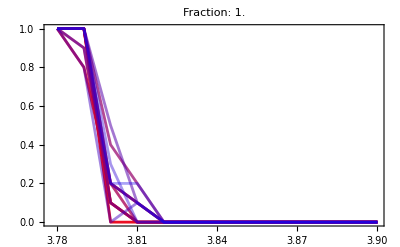

```mathematica
Table[ListPlot[Table[Table[{p0s[[p]],rigidRatio[[f,r,p]]},{p,Length[p0s]}],{r,Length[sizeRatio]}],PlotStyle->redBluePlotConfig[Length[sizeRatio]],PlotLabel->"Fraction: "<>ToString[fraction[[f]]],ImageSize->400,Joined->True,PlotRange->All],{f,Length[fraction]}]
```